```mathematica
NotebookDirectory[]
SetDirectory[NotebookDirectory[]]

FileNames[]
rawData=Import["accels.txt","CSV"];
```

J:\AcerWin8.1\Mark\Documents\Processing\HullPool\

J:\AcerWin8.1\Mark\Documents\Processing\HullPool

{accels.nb,accels.pdf,accels.txt,BuoyantBody.pde,configControls.pde,frames,GPPH (General Purpose Planing Hull - Original).IGS,GPPH (General Purpose Planing Hull Single Chine Variant - Working).3dm,GPPH (General Purpose Planing Hull Single Chine Variant - Working).3dmbak,GPPH (General Purpose Planing Hull - Working).3dm,GPPH(m - 0.2m slices).txt,GPPH (Single Chine) Savitsky Parameters.txt,HullBody.pde,HullPool.pde,PIDController.pde,Savitsky Lambda Based On Wetted Keel Length.nb,SutherlandHodgmanClipper.pde,ThrustPool.mov,ThrustPool.wmv,WaveBody.pde,Wave Impact Simulation_pptx,Wave Impact Simulation.pptx,WaveTank.pde}

```mathematica
Length[rawData]
rawData[[3]]
```

4470

{0.03,0.,0.0638992,-0.108081,-0.324604,-1.47964}

```mathematica
time=Table[rawData[[i]][[1]], {i, Length[rawData]-1}];
throttle=Table[rawData[[i]][[2]], {i, Length[rawData]-1}];
speed=Table[rawData[[i]][[3]], {i, Length[rawData]-1}];
trim=Table[rawData[[i]][[4]], {i, Length[rawData]-1}];
xAccel=Table[rawData[[i]][[5]], {i, Length[rawData]-1}];
yAccel=Table[rawData[[i]][[6]], {i, Length[rawData]-1}];
```

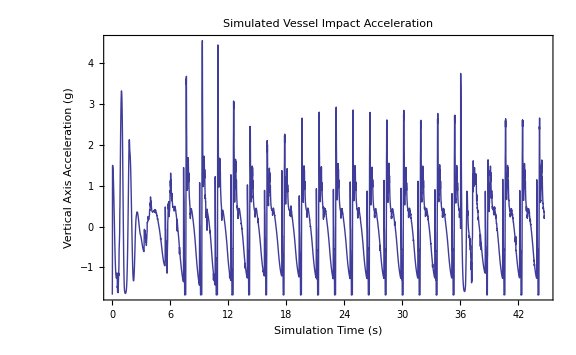

```mathematica
Table[{time[[i]], -yAccel[[i]]}, {i, Length[time]-1}];
ListLinePlot[%[[1;;]], ImageSize->Large, PlotRange->All, Frame->True, FrameLabel->{"Simulation Time (s)", "Vertical Axis Acceleration (g)"}, PlotLabel->"Simulated Vessel Impact Acceleration"]
```

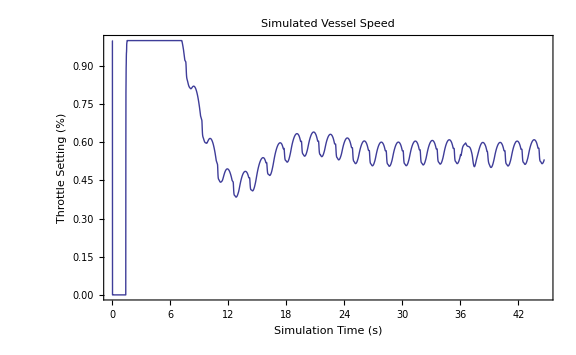

```mathematica
Table[{time[[i]], throttle[[i]]}, {i, Length[time]}];
ListLinePlot[%[[1;;]], ImageSize->Large, PlotRange->All, Frame->True, FrameLabel->{"Simulation Time (s)", "Throttle Setting (%)"}, PlotLabel->"Simulated Vessel Speed"]
```

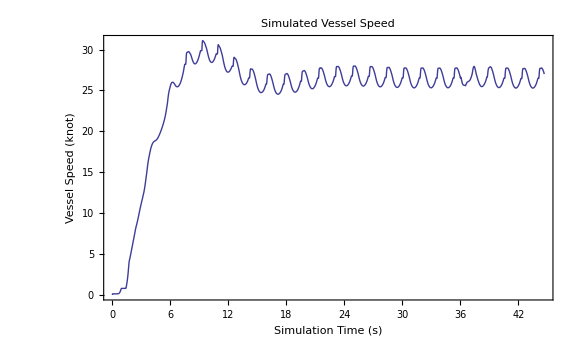

```mathematica
Table[{time[[i]], speed[[i]]*1.94384449}, {i, Length[time]}];
ListLinePlot[%[[1;;]], ImageSize->Large, PlotRange->All, Frame->True, FrameLabel->{"Simulation Time (s)", "Vessel Speed (knot)"}, PlotLabel->"Simulated Vessel Speed"]
```

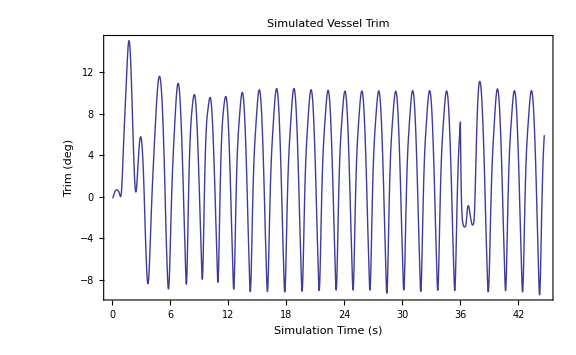

```mathematica
Table[{time[[i]], trim[[i]]}, {i, Length[time]}];
ListLinePlot[%[[1;;]], ImageSize->Large, PlotRange->All, Frame->True, FrameLabel->{"Simulation Time (s)", "Trim (deg)"}, PlotLabel->"Simulated Vessel Trim"]
```

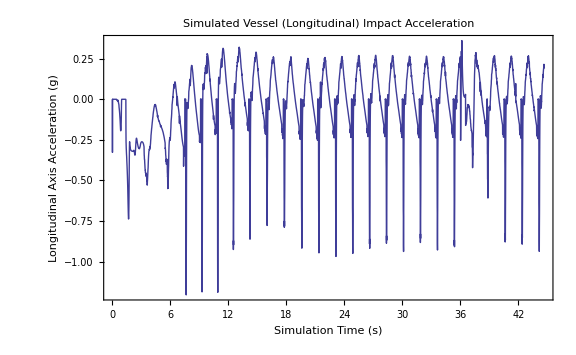

```mathematica
Table[{time[[i]], xAccel[[i]]}, {i, Length[time]}];
ListLinePlot[%[[1;;]], ImageSize->Large, PlotRange->All, Frame->True, FrameLabel->{"Simulation Time (s)", "Longitudinal Axis Acceleration (g)"}, PlotLabel->"Simulated Vessel (Longitudinal) Impact Acceleration"]
```